```mathematica
crit=.001^(.25);
fr=x/.Solve[x^2+.001/x^2==x,x,Reals][[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

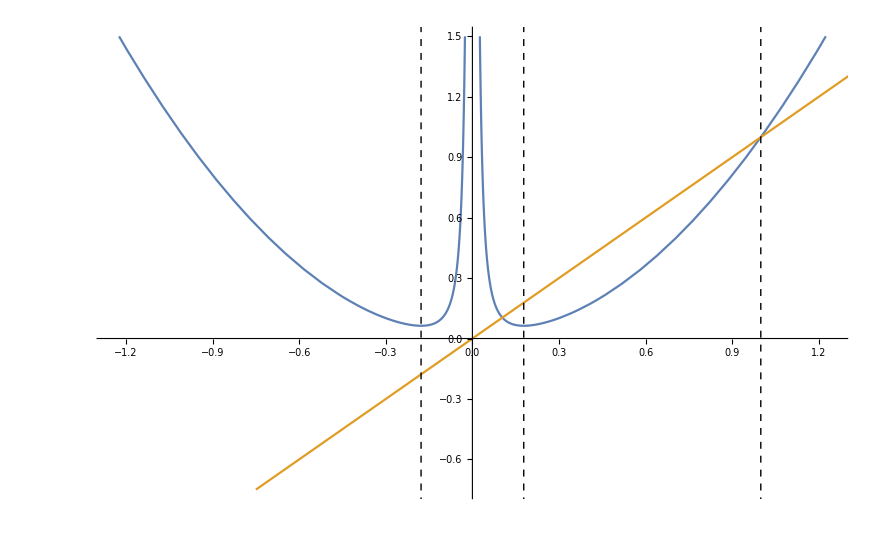

```mathematica
codings=Plot[{x^2+.001/x^2,x},{x,-1.5,1.5},PlotRange->{{-1.25,1.25},{-.75,1.5}},Epilog->{Dashed,Thick,Line[{{{-crit,-10},{-crit,10}},{{crit,-10},{crit,10}},{{fr,-10},{fr,10}}}]}]
```

```mathematica
Export["~/Mathematics/Dynamical_Research/paper/coding_diag.pdf",codings]
```

~/Mathematics/Dynamical_Research/paper/coding_diag.pdf

```mathematica
Solve[x^2+.001/x^2==x,x,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.103717},{x→0.998997}}

```mathematica
singpert[x_,c_,b_]:=x^2+c+b/(x^2)
```

```mathematica
sf = D[singpert[x,c,b ],{x,3}]/D[singpert[x,c,b ],{x,1}]-(3/2)(D[singpert[x,c,b ],{x,2}]/D[singpert[x,c,b ],{x,1}])^2
```

-(3 (2+(6 b)/x^4)^2)/(2 (-(2 b)/x^3+2 x)^2)-(24 b)/(x^5 (-(2 b)/x^3+2 x))

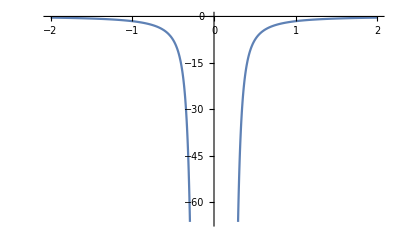

```mathematica
Plot[sf/.{c->-.1,b->.001}, {x,-2,2}]
```